```mathematica
Clear["Global`*"]
```

```mathematica
(*Plot*)
```

```mathematica
SetOptions[ListLinePlot,BaseStyle->{FontFamily->"Times",FontSize->40,FontColor->"Black"}];
```

```mathematica
name="time_0p2_10_N0100";
```

```mathematica
transitTime = Flatten[Import[NotebookDirectory[]<>name<>"/transitTime.dat"]];
intensitySS=Flatten[Import[NotebookDirectory[]<>name<>"/intensitySS.dat"]];
inversionSS=Flatten[Import[NotebookDirectory[]<>name<>"/inversionSS.dat"]];
nAtomSS=Flatten[Import[NotebookDirectory[]<>name<>"/nAtomSS.dat"]];
spinSpinCorSS=Flatten[Import[NotebookDirectory[]<>name<>"/spinSpinCorSS.dat"]];
intensityUnCorSS = Flatten[Import[NotebookDirectory[]<>name<>"/intensityUnCorSS.dat"]];
```

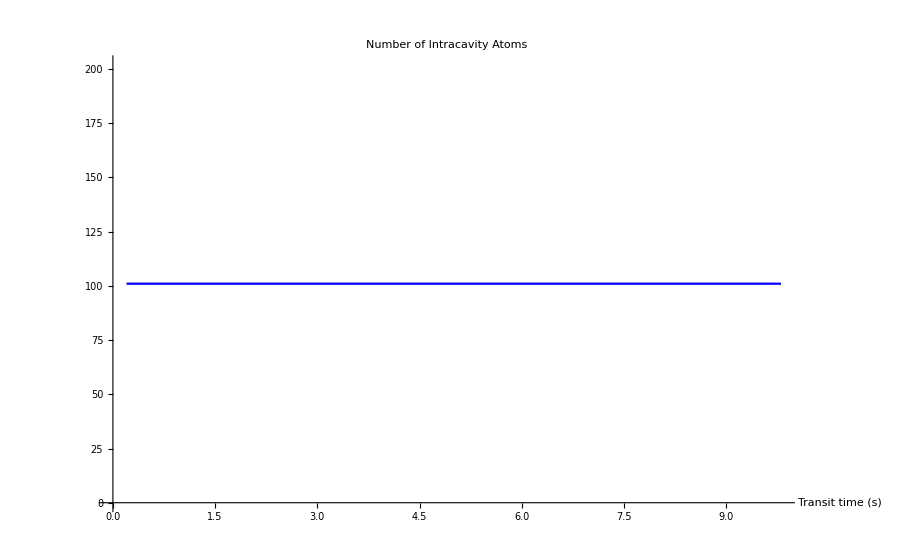

```mathematica
(*NAtom*)
nAtom = Transpose@{transitTime,nAtomSS};
plotNAtom=ListLinePlot[nAtom,PlotRange->All,PlotStyle->Blue,PlotLabel->"Number of Intracavity Atoms",AxesLabel->{"Transit time (s)"}]
```

```mathematica
(*Intensity*)
```

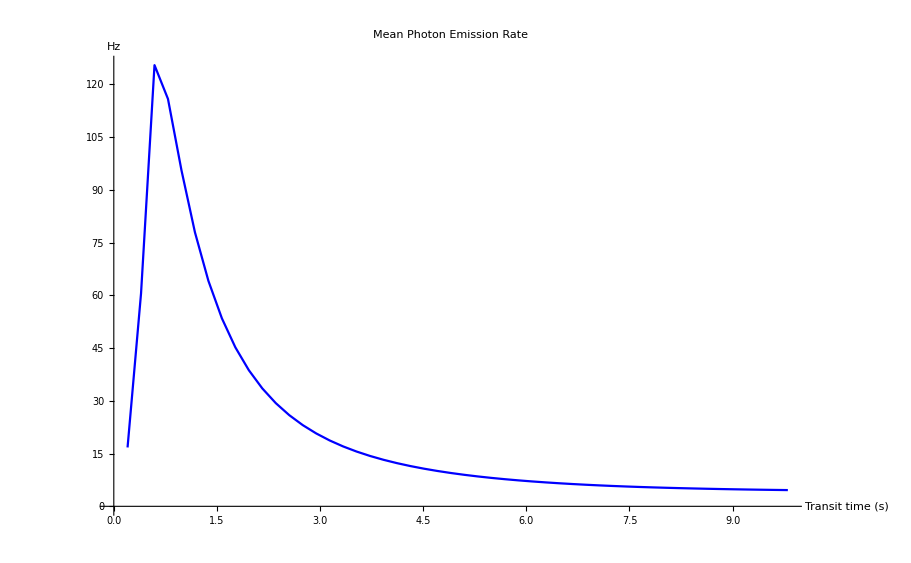

```mathematica
intensity = Transpose@{transitTime,intensitySS};
ListLinePlot[intensity,PlotRange->All,PlotStyle->Blue, PlotLabel->"Mean Photon Emission Rate",AxesLabel->{"Transit time (s)","Hz"}]
```

```mathematica
(*IntensityUnCor*)
```

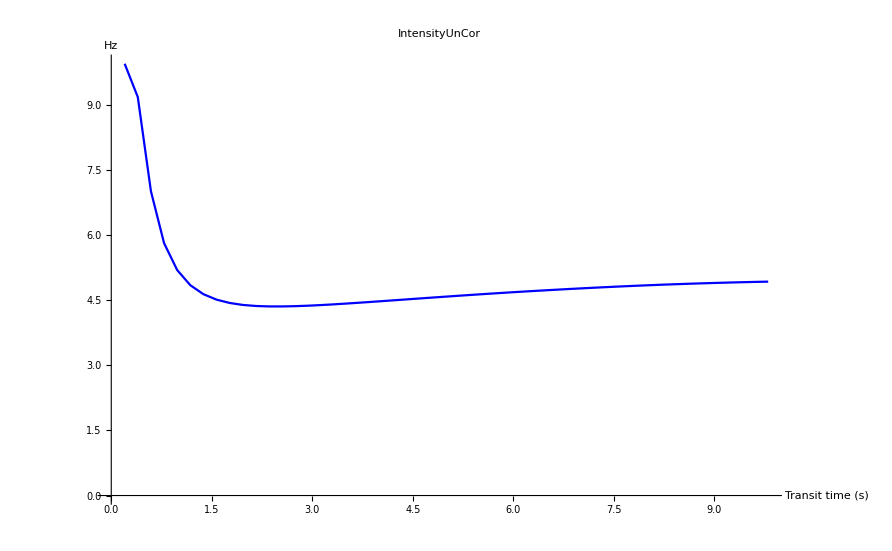

```mathematica
intensityUnCor = Transpose@{transitTime,intensityUnCorSS};
ListLinePlot[intensityUnCor,PlotRange->All,PlotStyle->Blue, PlotLabel->"IntensityUnCor",AxesLabel->{"Transit time (s)","Hz"}]
```

```mathematica
(*Intensity v.s. IntensityUnCor*)
```

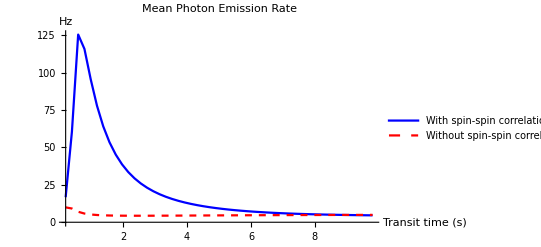

```mathematica
plotBothIntensity=ListLinePlot[{intensity,intensityUnCor},PlotStyle->{{Blue},{Red,Dashed}}, PlotLabel->"Mean Photon Emission Rate",AxesLabel->{"Transit time (s)","Hz"},PlotRange->All,AxesOrigin->{0.2,0},PlotLegends->{"With spin-spin correlations","Without spin-spin correlations"}]
```

```mathematica
(*Inversion*)
```

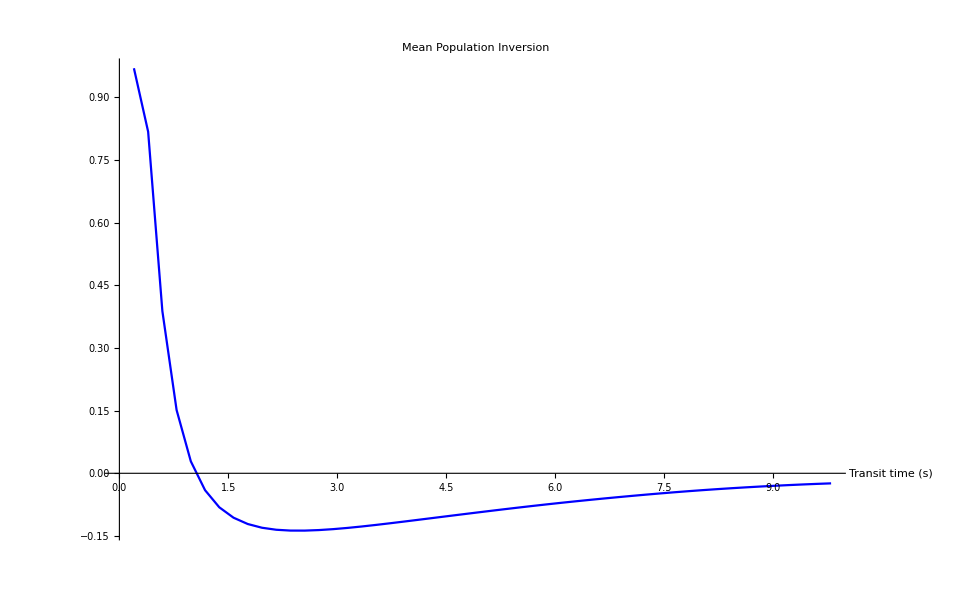

```mathematica
inversion= Transpose@{transitTime,inversionSS};
plotInversion=ListLinePlot[inversion,PlotRange->All,PlotStyle->Blue, PlotLabel->"Mean Population Inversion",AxesLabel->{"Transit time (s)"}]
```

```mathematica
(*spinSPinCor*)
```

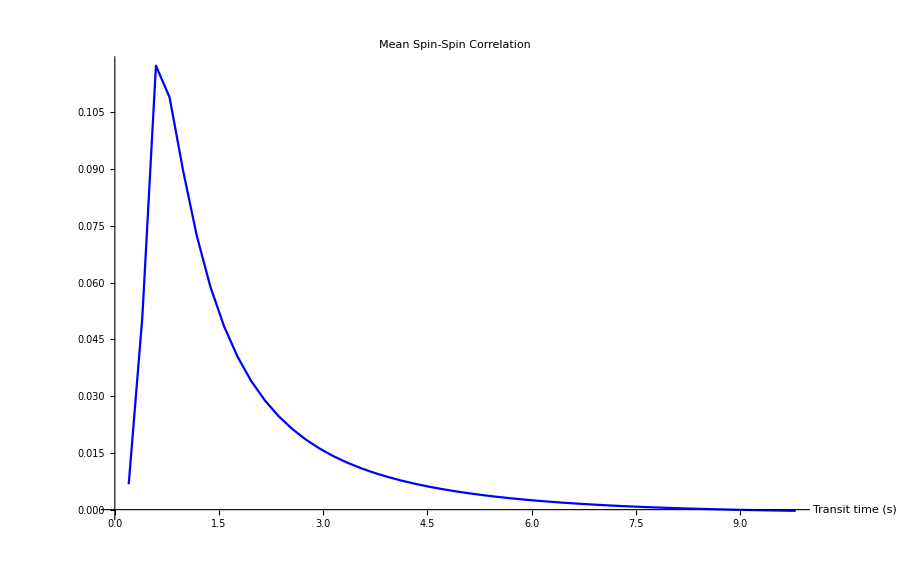

```mathematica
spinSpinCor  = Transpose@{transitTime,spinSpinCorSS};
plotSpinSpinCor=ListLinePlot[spinSpinCor,PlotRange->All,PlotStyle->Blue,PlotLabel->"Mean Spin-Spin Correlation",AxesLabel->{"Transit time (s)"}]
```